## §6. Вычеты и их применение.

### 6.1. Вычет функции и его вычисление.

Если функция f(z) аналитична в некоторой окрестности точки z_0, за исключением может быть самой точки z_0, то вычетом функции f(z) относительно точки z_0, обозначаемым res[f(z), z→ z_0]или res[f(z),z_0] называется число, равное значению интеграла 1/(2π ⅈ)∫_C f(z)ⅆz, где С - некоторый замкнутый контур, лежащий в области аналитичности f(z) и содержащий внутри себя только одну особую точку z_0.

Вычет функции совпадает с коэффициентом с_-1 разложения f(z) в ряд Лорана по степеням z - z_0, т.е.

res[f(z),z_0]=c_-1=1/(2 π ⅈ)∫_(|z-z_0|=r) f(z)ⅆz

Если z_0=∞ - изолированная особая точка функции f(z), то

res[f(z),∞]=1/(2 π ⅈ)∫_(С_R^-) f(z)ⅆz

где С_R^-={z| |z|=R}, R достаточно велико и обход контура - по часовой стрелке. Заметим, что если

f(z)=∑_(n=-∞)^∞ c_n z^n,          r< |z| <∞,
c_n=1/(2 π ⅈ)∫_(|z|=R>r) (f(z))/z^(n+1)ⅆz, n= 0,±1,±2,  то

res[f(z),∞]=-с_-1.

Если z_0 - полюс первого порядка функции f(z), то

res[f(z),z_0]=lim_(z→z_0) (z-z_0)f(z)

Если z_0- полюс порядка m≥2 функции f(z), то

res[f(z),z_0]=1/((m-1)!)  lim _(z→z_0) ⅆ^(m-1)/(ⅆ z^(m-1)) ((z-z_0)^m f(z))

##### Пример №12.416

Найти вычеты указанной функции относительно каждого из его полюсов, отличных от ∞

f(z)=ⅇ^z/(z^2(z^2+9))

Найдем каждый полюс заданной функции:

```mathematica
f[z_]:=E^z/(z^2(z^2+9))
```

Для того чтобы найти особые точки функции f(z), решим уравнение вида: (f(z))^-1=0.

```mathematica
sol=z/.Solve[f[z]^-1==0,z]
```

{0,0,-3 ⅈ,3 ⅈ}

Для того чтобы найти вычет в точке, воспользуемся функцией Residue[f[z],{z,z_0}], которая находит вычет функции f(z) в точке z_0.

```mathematica
Residue[f[z],{z,0}]
```

1/9

Это можно проделать для каждого полюса, но если представить, что имеется очень много полюсов, то искать вычет в каждом отдельно - довольно трудоемкая задача.

Найдем вычеты сразу во всех точках множества полюсов.

```mathematica
Table[ {sol[[i]],Residue[f[z],{z,sol[[i]]}]},{i,1,Length[sol]}] // DeleteDuplicates
```

{{0,1/9},{-3 ⅈ,-1/54 ⅈ ⅇ^(-3 ⅈ)},{3 ⅈ,1/54 ⅈ ⅇ^(3 ⅈ)}}

Элементы данного множества имеют вид: z_0 , res(f(z), z_0).

Получили три полюса, причем один из них второго порядка (z_0=0), и вычеты в каждом из них.

##### Пример №12.413

Найти вычеты указанной функции относительно каждого из его полюсов, отличных от ∞

f(z)=1/(sin(z)-1/2)

Запишем функцию f(z) и найдем полюса, решив уравнение (f(z))^-1=0:

```mathematica
f[z_]:=1/(Sin[z]-1/2)
```

```mathematica
sol=Solve[f[z]^-1==0,z]
```

{{z→ConditionalExpression[π/6+2 π C[1],C[1]∈Integers]},{z→ConditionalExpression[(5 π)/6+2 π C[1],C[1]∈Integers]}}

Получили бесконечное число решений, следовательно и полюсов. Перепишем решение в более привычный для нас вид:

```mathematica
sol1={{z-> π/6+2π n},{z-> (5π)/6+2π n}};
```

Или, если записать одним выражением:

```mathematica
sol2=(-1)^n π/6+π n;
```

Если функция периодична, то и функция вычета от  n также будет периодичной. Докажем это составив множество {z_0(n), Res(f(z), z→z_0(n))}

```mathematica
Table[{sol2,Residue[f[z],{z,sol2}]},{n,-3,3}]
```

{{-(19 π)/6,-2/(√3)},{-(11 π)/6,2/(√3)},{-(7 π)/6,-2/(√3)},{π/6,2/(√3)},{(5 π)/6,-2/(√3)},{(13 π)/6,2/(√3)},{(17 π)/6,-2/(√3)}}

Ответ:

res[f(z),(-1)^n π/6+π n]=(-1)^n 2/(√3)

В таком же порядке следует решать задачи №№12.408-12.423.

##### Общий алгоритм

Составим программный модуль, который для любой функции f(z) в кольце |z-a|<b будет находить все полюса, а затем вычислять в них вычет.

Действовать он будет следующим образом:

1. Решение уравнения f^-1(z)=0  при условии |z_k-a|<b.

2. Составление множества типа {z_k,res[f(z),z_k]}

```mathematica
residueK[z_,func_,a_,b_]:=Module[{sol},
sol=z/.Solve[Abs[z-a]<b&&func^-1==0,z]//DeleteDuplicates;
Table[{sol[[i]],Residue[func,{z,sol[[i]]}]},{i,1,Length[sol]}]
]
```

Продемонстрируем пример его работы:

```mathematica
residueK[z,E^z/(z^2(z^2+9)),0,10]
```

{{0,1/9},{-3 ⅈ,-1/54 ⅈ ⅇ^(-3 ⅈ)},{3 ⅈ,1/54 ⅈ ⅇ^(3 ⅈ)}}

```mathematica
residueK[z,1/(Sin[z]-1/2),0,10]
```

{{-(19 π)/6,-2/(√3)},{-(11 π)/6,2/(√3)},{-(7 π)/6,-2/(√3)},{π/6,2/(√3)},{(5 π)/6,-2/(√3)},{(13 π)/6,2/(√3)},{(17 π)/6,-2/(√3)}}

Примечание: Данный модуль работает лишь с теми функциями, в которых полюс является нулём функции g(z)=f^-1(z). С более сложными функциями он справиться не может.

Рассмотрим следующий номер:

##### Пример №12.424

Найти вычеты функции относительно точки z_0=0:

f(z)=e^(1/z), z_0=0

Введем заданную функцию:

```mathematica
f[z_]:=Exp[1/z]
```

Точка z_0=0 для нее является существенно особой, так как не существует предела функции при z→ z_0 :

```mathematica
Limit[Cos[1/z]+I Sin[1/z],z->0]
```

ⅈ Interval[{-1,1}]+Interval[{-1,1}]

Попытаемся воспользоваться встроенной функцией Residue:

```mathematica
Residue[f[z],{z,0}]
```

Residue[ⅇ^(1/z),{z,0}]

Никакого результата мы не получили.

Для нахождения вычета определим коэффициент c_-1 разложения функции e^(1/z) в ряд Лорана по степеням z .

Функция разложения в ряд Series также не дала нам нужного результата.

```mathematica
Series[f[z],{z,0,4}]
```

ⅇ^(1/z)

Известно разложение в ряд функции ⅇ^η:

ⅇ^η=∑_(n=0)^∞ η^n/(n!)

а также то, что данный ряд сходится на всей комплексной плоскости. Поэтому заменим η=1/z. Тогда получается ряд:

ⅇ^(1/z)=∑_(n=0)^∞ 1/(n!)(1/z)^n

Запишем это разложение следующим образом:

```mathematica
Normal[Series[Exp[p],{p,0,4}]]/.p-> 1/z
```

1+1/(24 z^4)+1/(6 z^3)+1/(2 z^2)+1/z

Отсюда видно, что  коэффициент c_-1=1. Следовательно ответ:

res(e^(1/z),z→0)=1

Примечание: номера №12.425,426 имеют точно такой же ход решения, поэтому рекомендуются к самостоятельному решению.

##### Пример №12.427

Найти вычеты функции относительно точки z_0=∞

f(z)=sin(1/z), z_0=∞

Имеем функцию:

```mathematica
f[z_]:=Sin[1/z]
```

Решим задачу при помощи разложения функции в ряд Лорана.

Имеем стандартное разложение:

sin(η)=∑_(n=0)^∞ (-1)^n η^(2n+1)/((2n+1)!)

Произведя замену η→ 1/z, получаем:

sin(1/z)=∑_(n=0)^∞ (-1)^n(1/z)^(2n+1)/((2n+1)!)

Получим это разложение:

```mathematica
Normal[Series[Sin[p],{p,0,7}]]/.p-> 1/z
```

-1/(5040 z^7)+1/(120 z^5)-1/(6 z^3)+1/z

Вычет в бесконечно удаленной точке по формуле (3) равен:

res(f(z),z→∞)=-c_-1

поэтому, исходя  разложения в ряд, получаем ответ:

res(sin(1/z),z→∞)=-1

Проверим себя при помощи функции Residue:

```mathematica
Residue[Sin[1/z],{z,Infinity}]
```

-1

Получили верный ответ.

##### Пример №12.428

Найти вычеты функции относительно точки z_0=∞

f(z)=1/((z-1)^2(z^2+1)), z_0=∞

Дана функция:

```mathematica
f[z_]:=1/((z-1)^2(z^2+1))
```

Найдем вычет в бесконечно удаленной точке, как:

res(f(z),z→∞)=-c_-1

Для этого воспользуемся полученным нами в разделе Ряды Лорана модулем, который мы назвали loran[z,f[z],z0,r,k]:

```mathematica
loranO[z,f[z],0,100,7]
```

2/z^7+2/z^6+2/z^5+1/z^4

Примечание: для того чтобы воспользоваться функцией loranO сначала ее нужно определить.

Видим что коэффициент перед 1/z отсутствует, следовательно ответ:

res(1/((z-1)^2(z^2+1)),∞)=0

Также можно напрямую воспользоваться функцией Residue и получить тот же ответ:

```mathematica
Residue[1/((z-1)^2(z^2+1)),{z,Infinity}]
```

0

### 6.2. Теоремы о вычетах и их применение к вычислению контурных интегралов.

П е р в а я  т е о р е м а  о  в ы ч е т а х. Если функция f(z) аналитична в области D, за исключением изолированных особых точек z_1,... z_k, лежащих в этой области, то для любого простого замкнутого контура C⊂D, охватывающего точки z_1,... z_N:

∫_(С^+) f(z)ⅆz=2πⅈ∑_(k=1)^N res(f(z);z_k)

В т о р а я  т е о р е м а  о  в ы ч е т а х.  Если функция f(z) аналитична во всей комплексной плоскости, за исключением изолированных особых точек z_1,... z_(N-1), и z_N=∞, то:

∑_(k=1)^N res(f(z);z_k)=0

##### Пример №12.434

Используя теоремы о вычетах, вычислить следующий интеграл:

∫_(C^+) z/((z-1)(z-2))ⅆz,  C={z | |z-2|=2}

Для того чтобы решить поставленную задачу, воспользуемся Первой теоремой о вычетах:

Найдем все полюса функции f(z)

```mathematica
f[z_]:=z/((z-1)(z-2))
```

1) Приведем графическое решение:

Найдем полюса:

```mathematica
sol=z/.Solve[f[z]^-1==0,z]
```

{1,2}

Для этого изобразим контур С, и полюса z=1, z=2.

```mathematica
Show[ ContourPlot[(x-2)^2+y^2==4,{x,0,4},{y,-2,2},AxesLabel->{Re,Im},PlotRange->{{-1,5},{-3,3}} ,Frame->False,Axes->True],Graphics[{PointSize[Large],Point[ReIm[sol]]} ] ]
```

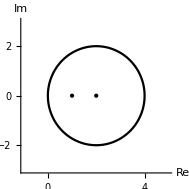

Из рисунка видно, что обе точки лежат внутри контура С.

Найдем интеграл по первой теореме вычетов.

```mathematica
int=2π ⅈ Sum[Residue[f[z],{z,sol[[i]]}],{i,1,Length[sol]}]
```

2 ⅈ π

2) Воспользуемся написанной нами в главе 1 параграфе 4 программой integrateC[z,f[z],a,b]:

```mathematica
integrateC[z,f[z],2,2]
```

2 ⅈ π

Получили тот же самый ответ.

3) Применим новый подход с использованием вычетов. Для этого воспользуемся программой, написанной в предыдущем разделе, residueK[z,f[z],a,b]. Она находит полюса и вычеты в них:

```mathematica
res=residueK[z,f[z],2,2]
```

{{1,-1},{2,2}}

Напомним, что элемент данного множество имеет вид: {z_k,res[f(z),z_k]}

Теперь, для того чтобы найти значение интеграла, воспользуемся первой теоремой о вычетах (6):

```mathematica
int=2I Pi Sum[res[[i,2]],{i,1,Length[res]}]
```

2 ⅈ π

С использованием изложенных выше способов читателю рекомендуется решить задания №№ 12.435-449 самостоятельно.

##### Общий алгоритм

Составим новый программный модуль, взамен старого integrateC[z,f[z],a,b], который будет иметь те же входные параметры, но использовать первую теорему о вычетах:

```mathematica
integrateR[z_,func_,a_,b_]:=Module[{sol},
sol=z/.Solve[Abs[z-a]<b&&func^-1==0,z]//DeleteDuplicates;
2 I Pi Sum[Residue[func,{z,sol[[i]]}],{i,1,Length[sol]}]]
```

Продемонстрируем пример работы:

##### Пример №12.433

```mathematica
-integrateR[z,1/(z^4+1),1,1]//Simplify
```

(ⅈ π)/(√2)

##### Пример №12.436

```mathematica
integrateR[z,Sin[z]/(z^2+9),0,4]
```

2/3 ⅈ π Sinh[3]

##### Пример №12.441

```mathematica
integrateR[z,(z+1)/(Exp[z]+1),0,4]//Simplify
```

-4 ⅈ π

##### Пример №12.437

Используя теоремы о вычетах, вычислить следующий интеграл:

∮ⅆz/((z-a)^n(z-b)^n), C={ z | |z|=1}, n ∈ℕ, 0≤ |a|<1< |b|

Из условий видно, что a - полюс n-ого порядка, который лежит внутри контура С.

Зададим функцию f(z,n) и попробуем найти вычет в точке а с помощью уже хорошо знакомой нам функции Residue:

```mathematica
f[z_,n_]:=1/((z-a)^n(z-b)^n)
```

```mathematica
Residue[f[z,n],{z,a}]
```

Residue[(-a+z)^-n (-b+z)^-n,{z,a}]

В общем виде результат мы не получили.

Теперь попробуем воспользоваться определением вычета:

res[f(z),z_0]=1/((n-1)!)lim_(z→z_0) ⅆ^(n-1)/(ⅆ z^(n-1))[(z-z_0)^n f(z)]

Зададим вычет, как функцию от n:

```mathematica
res1[n_]:=1/((n-1)!)Limit[D[(z-a)^n f[z,n],{z,n-1}],z->a]
```

```mathematica
res1[n]
```

Limit[∂_{z,-1+n} (-b+z)^-n,z→a]/((-1+n)!)

Результат в общем виде мы снова не получили. Зато можем увидеть, как зависит вычет от n:

```mathematica
Table[res1[i],{i,1,5}]
```

{1/(a-b),-2/(a-b)^3,6/(a-b)^5,-20/(a-b)^7,70/(a-b)^9}

Из определения вычета видно:

res[f(z),a]=1/((n-1)!)lim_(z→a) ⅆ^(n-1)/(ⅆ z^(n-1))[1/(z-b)^n]

Запишем:

ⅆ^(n-1)/(ⅆ z^(n-1))[1/(z-b)^k]=(-1)^(n-1)(k(k+1)...(k+n-2))/(z-b)^(k+n-1)=(-1)^(n-1)(n(n+1)...(2n-2))/(z-b)^(2n-1)

Значит:

res[f(z),a]=(-1)^(n-1)/((n-1)!)(n(n+1)...(2n-2))/(a-b)^(2n-1)

И тогда:

∮ⅆz/((z-a)^n(z-b)^n)=2π ⅈ(-1)^(n-1)/((n-1)!)(n(n+1)...(2n-2))/(a-b)^(2n-1) ,n ∈ℕ, 0≤ |a|<1< |b|

##### Пример №12.438

Изменим условия предыдущей задачи на:

0≤ |a|< |b|<1

Тогда ввиду симметрии задачи:

res[f(z),b]=(-1)^(n-1)/((n-1)!)(n(n+1)...(2n-2))/(b-a)^(2n-1)

∮ⅆz/((z-a)^n(z-b)^n)=2π ⅈ((-1)^(n-1)/((n-1)!)(n(n+1)...(2n-2))/(a-b)^(2n-1)+(-1)^(n-1)/((n-1)!)(n(n+1)...(2n-2))/(b-a)^(2n-1))=((-1)^(n-1)/((n-1)!)(n(n+1)...(2n-2))/((-1)^(2n-1)(b-a)^(2n-1))+(-1)^(n-1)/((n-1)!)(n(n+1)...(2n-2))/(b-a)^(2n-1))=(-(-1)^(n-1)/((n-1)!)(n(n+1)...(2n-2))/(b-a)^(2n-1)+(-1)^(n-1)/((n-1)!)(n(n+1)...(2n-2))/(b-a)^(2n-1))=0

Следовательно:

∮ⅆz/((z-a)^n(z-b)^n)=0, n ∈ℕ, 0≤ |a|< |b|<1

### 6.3. Применение вычетов к вычислению определенных интегралов.

I. Интегралы вида:

∫_0^(2π) R(sin(x),cos(x))ⅆx

где R- символ рациональной функции, с помощью замены вида z=e^(ⅈ x)приводятся к контурным интегралам от рациональных относительно z функций.

##### Пример №14.450

Используя метод описанный выше, вычислить определенный интеграл:

∫_0^(2π) 1/(a+b cos(x))^2 ⅆx, a>b>0

Запишем функцию:

```mathematica
f[x_]:=1/(a+b Cos[x])^2
```

Мы конечно же можем  вычислить данный интеграл напрямую:

```mathematica
Assuming[0<b&&a>b&&x∈Reals,Integrate[f[x],{x,0,2 Pi}]]//Timing
```

{7.95605,(2 a π)/((a^2-b^2)^(3/2))}

но на вычисление такого простого интеграла “в лоб” Mathematica затрачивает целых 8 секунд, значит на более сложные интегралы времени уйдет еще больше, так что попробуем упростить задачу заменой описанной выше.

Произведем замену:

ⅇ^(ⅈ x)=z,ⅆx=ⅆz/(ⅈ z)

Тогда получим:

```mathematica
Simplify[TrigToExp[f[x]]*1/(I z)/.<|E^(I x)-> z,E^(-I x)->1/z|>]
```

-(4 ⅈ z)/((b+2 a z+b z^2)^2)

Напомним: функция TrigToExp записывает тригонометрические функции через экспоненциальные, множитель 1/(ⅈ z) следует из (11).

Запишем функцию f_1(z):

```mathematica
f1[z_]:=-(4 I z)/((b+2 a z+b z^2)^2)
```

Найдем полюса из уравнения (f_1(z))^-1=0 при условии, что |z_k|<1, а также a>b, b>0

```mathematica
sol=z/.DeleteDuplicates[Solve[a>b&&b>0&&Abs[z]<1&&f1[z]^-1==0,z]]//Simplify
```

{ConditionalExpression[√(-1+a^2/b^2)-a/b,b>0&&a>b]}

Получили один полюс:

```mathematica
z1=√(-1+a^2/b^2)-a/b;
```

Теперь воспользовавшись первой теоремой о вычетах найдем значение интеграла и время, за которое он вычисляется:

```mathematica
int=2ⅈ π Residue[f1[z],{z,z1}]//Timing
```

{0.0156001,-(2 a π)/(√(-1+a^2/b^2) b (-a^2+b^2))}

Теперь осталось преобразовать ответ, чтобы убедиться, что он совпадает с ответом полученным “в лоб”:

```mathematica
Simplify[int[[2]],a>b&&b>0]
```

(2 a π)/((a^2-b^2)^(3/2))

Мы получили тот же ответ, но за значительно меньший промежуток времени.

Окончательный ответ:

∫_0^(2π) 1/(a+b cos(x))^2 ⅆx=(2 a π)/((a^2-b^2)^(3/2))

Данным алгоритмом можно считать любые интегралы вида:

∫_0^(2π) R(sin(x),cos(x))ⅆx

Остальные номера, №№12.450-455, рекомендуются к самостоятельному выполнению ввиду своего однообразия.

II. Интегралы вида:

∫_(-∞)^∞ f(x)ⅆx

где f(x) - функция непрерывная на  (-∞;∞), аналитическая в верхней полуплоскости, за исключением конечного числа особых точек z1....zn, лежащих в конечной части верхней полуплоскости, вычисляются:

∫_(-∞)^∞ f(x)ⅆx=2π ⅈ∑_(i=1)^n res(f(z), z_i)

##### Пример №12.461

Вычислить интеграл, используя описанный выше способ:

∫_(-∞)^∞ (x^4+1)/(x^6+1)ⅆx

Зададим функцию

```mathematica
f[x_]:=(x^4+1)/(x^6+1)
```

Вычислим интеграл с помощью функции Integrate и измерим время.

```mathematica
Integrate[f[x],{x,-Infinity,Infinity}]//Timing
```

{0.202801,(4 π)/3}

Сравним  время, затрачиваемое на вычисление данного интеграла “в лоб”, с временем, требуемым для решения данной задачи способом описанным выше.

Для этого найдем все полюса, лежащие в верхней полуплоскости ( Im[z]>0):

```mathematica
sol=z/.Solve[Im[z]>0&&f[z]^-1==0,z]
```

{ⅈ,(-1)^(1/6),(-1)^(5/6)}

Изобразим их на комплексной плоскости:

```mathematica
Graphics[{PointSize[Large],Point[ReIm[sol]]},Axes->True,PlotRange->{{-1,1},{0,2}},AxesLabel->{Re,Im}]
```

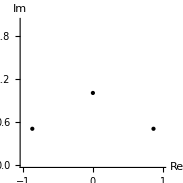

Теперь найдем значение интеграла согласно (12):

```mathematica
int=2 ⅈ π Sum[Residue[f[z],{z,sol[[i]]}],{i,1,Length[sol]}]//ComplexExpand//Timing
```

{0.,(4 π)/3}

Получили тот же ответ, но время, затраченное на его вычисление, пренебрежимо мало.

Итак, имеем:

∫_(-∞)^∞ f(x)ⅆx=(4 π)/3

Способы, описанные выше, можно применить ко всем задачам №№12.450-470, что и рекомендуется сделать самостоятельно.

### 6.4. Разложение в ряд Лорана по методу вычетов

Вычет функции в точке равен коэффициенту c_-1 разложения в ряд Лорана, значит, если идти в обратном направлении, можно найти этот коэффициент. Воспользуемся этим для того, чтобы написать модуль разложения функции в ряд Лорана. Рассмотрим пример.

##### Пример №12.357

Найти все разложения указанной функции в ряд Лорана по степеням z-z_0 и установить области сходимости:

f(z)=(z+1)/(z^2-3z+2), z_0=1

Запишем функцию:

```mathematica
f[z_]:=(z+1)/(z^2-3z+2)
```

Получим множество особых точек:

```mathematica
sol=z/.Solve[z^2-3z+2==0,z]
```

{1,2}

Точка z_0 является полюсом первого порядка. Для того чтобы вычислить коэффициент Лорана, нам нужно вычислить интеграл:

c_n=1/(2π ⅈ)∮_(|z-1|=r') (f(z))/(z-1)^(n+1)ⅆz,     где 0<r'<1

Вычет по определению равен:

res[f(z),1]=c_-1=1/(2 π ⅈ)∮_(|z-z_0|=r') f(z)ⅆz

Отсюда следует, что если мы будем применять функцию Residue к функции f(z)/(z-z_0)^(n+1) , то будем получать n-ый коэффициент Лорана:

res[(f(z))/(z-1)^(n+1),1]=c_n=1/(2 π ⅈ)∮_(|z-z_0|=r') (f(z))/(z-1)^(n+1)ⅆz

Итак, запишем функцию n-ого коэффициента при разложении вблизи точки z_0:

```mathematica
c[n_]:=Residue[f[z]/(z-1)^(n+1),{z,1}]
```

Получим разложение в ряд:

```mathematica
Sum[c[n](z-1)^n,{n,-5,5}]
```

-3-2/(-1+z)-3 (-1+z)-3 (-1+z)^2-3 (-1+z)^3-3 (-1+z)^4-3 (-1+z)^5

Сравним ответ с результатом работы функции loranO:

```mathematica
loranO[z,f[z],1,1/2,5]
```

-3-2/(-1+z)-3 (-1+z)-3 (-1+z)^2-3 (-1+z)^3-3 (-1+z)^4-3 (-1+z)^5

и с результатом Series:

```mathematica
Series[f[z],{z,1,5}]
```

-2/(z-1)-3-3 (z-1)-3 (z-1)^2-3 (z-1)^3-3 (z-1)^4-3 (z-1)^5+O[z-1]^6

Во всех случаях получили одинаковый ответ.

Теперь получим коэффициент разложения в кольце с радиусом r>1:

c_n=1/(2π ⅈ)∮_(|z-1|=R) (f(z))/(z-1)^(n+1)ⅆz,     где R>1

Согласно первой теореме вычетов этот интеграл будет равен:

1/(2π ⅈ)∮_(|z-1|=R) (f(z))/(z-1)^(n+1)ⅆz=∑_(k=1)^N res[(f(z))/(z-1)^(n+1);z_k]

где z_k- полюса, охватываемые контуром интегрирования.

Отсюда,  n-ый коэффициент будем искать по формуле:

c_n=res[(f(z))/(z-1)^(n+1),1]+∑_(k=1)^N res[(f(z))/(z-1)^(n+1);z_k],     где R>1

где z_k- полюса, охватываемые контуром интегрирования R, за исключением полюса z_0.

Итак, первое слагаемое у нас уже вычислено, осталось найти второе:

```mathematica
c1[n_]:=Residue[f[z]/(z-1)^(n+1),{z,2}]
```

Теперь чтобы получить разложение в ряд Лорана в кольце R>1:

```mathematica
Sum[(c[n]+c1[n])(z-1)^n,{n,-5,5}]
```

3/(-1+z)^5+3/(-1+z)^4+3/(-1+z)^3+3/(-1+z)^2+1/(-1+z)

Сравним ответы:

```mathematica
loranO[z,f[z],1,3,5]
```

3/(-1+z)^5+3/(-1+z)^4+3/(-1+z)^3+3/(-1+z)^2+1/(-1+z)

Так как функции Series и SeriesCoefficient работают быстрее всего, то рациональнее по возможности использовать их. Коэффициент c_n вблизи точки z_0 оптимальнее искать именно с помощью функции SeriesCoefficient.

Соберем всё это в единый модуль:

```mathematica
loranR[expr_,{z_,z0_,k_},r_]:=Module[{sol,c,c1},
sol=z/.Solve[0<Abs[z-z0]<r&&Denominator[Simplify[TrigToExp[expr]]]==0,z];
c[n_]:=Evaluate[SeriesCoefficient[expr,{z,z0,n}]];
If[Length[sol]≠0,
sol=DeleteDuplicates[sol];
c1[n_]:=Sum[Residue[expr/(z-z0)^(n+1),{z,sol[[i]]}],{i,1,Length[sol]}],c1[n_]:=0;];
Sum[(c1[n]+c[n])(z-z0)^n,{n,-k,k}]]
```

##### Пример №12.364

```mathematica
loranR[z/((z^2+1)^2),{z,I,5},1/2]
```

-ⅈ/16-ⅈ/(4 (-ⅈ+z)^2)+1/16 (-ⅈ+z)+3/64 ⅈ (-ⅈ+z)^2-1/32 (-ⅈ+z)^3-5/256 ⅈ (-ⅈ+z)^4+3/256 (-ⅈ+z)^5

```mathematica
loranR[z/((z^2+1)^2),{z,I,8},3]
```

-(112 ⅈ)/(-ⅈ+z)^8+48/(-ⅈ+z)^7+(20 ⅈ)/(-ⅈ+z)^6-8/(-ⅈ+z)^5-(3 ⅈ)/(-ⅈ+z)^4+1/(-ⅈ+z)^3

##### Пример №12.375

```mathematica
loranR[1/((z^2-4)(z^2-1)),{z,0,8},1/2]
```

1/4+(5 z^2)/16+(21 z^4)/64+(85 z^6)/256+(341 z^8)/1024

```mathematica
loranR[1/((z^2-4)(z^2-1)),{z,I,5},3/2]
```

-1/15+2/(3 (-ⅈ+z)^4)+(2 ⅈ)/(3 (-ⅈ+z)^3)-1/(3 (-ⅈ+z)^2)-2/75 ⅈ (-ⅈ+z)-1/375 (-ⅈ+z)^2-4/625 ⅈ (-ⅈ+z)^3+(19 (-ⅈ+z)^4)/9375-(22 ⅈ (-ⅈ+z)^5)/46875

```mathematica
loranR[1/((z^2-4)(z^2-1)),{z,I,8},5/2]
```

-49/(-ⅈ+z)^8-(10 ⅈ)/(-ⅈ+z)^7-5/(-ⅈ+z)^6-(4 ⅈ)/(-ⅈ+z)^5+1/(-ⅈ+z)^4

Сравним скорость работы этой функции и функции loranO при больших степенях разложения:

```mathematica
Timing[loranR[z/((z^2+1)^2),{z,I,500},5/2];]
```

{0.561604,Null}

```mathematica
Timing[loranO[z,z/((z^2+1)^2),I,5/2,500];]
```

{7.17605,Null}

Так как функция loranR работает быстрее, предпочтение в использовании будем отдавать именно ей.